```mathematica
ClearAll
listH ={100,100,100} (*мощности слоев*)
slope = {10 Degree,-10 Degree, 20Degree} (*наклон слоев*)
len = 1000(*длина профиля*)
dx = 5(*шаг по профилю*)
hDispersion = 0(*степень складчатости нижнего слоя в метрах*)
hTapering =5  (*степень влияния нижнего горизонта на верхние*)
listV = {1000,2000,3000, 4000} (*набор скоростей*)
wellCount= 10 (*кол скважин*)
wellType = "max" (*расположение скважин "max","min","regular","random"*)
type = 1 (*выполаживание. 1 - кверху, -1 - книзу*)

Build[listH_, slope_, len_, dx_, hDispersion_, hTapering_, type_] := 
Module[{
                i,
                horizons,
                radius,
                parametres,
                surface,    
                data,
                anomaly, 
                anomalyFiltered,
                listSumH,
                flat,
                inclined,
                totalH,
                max
},
				If[hTapering >= 1/2 ((len/dx) - radius) listH[[1]]/totalH , Return["hTapering is too big"]]; 
 
				radius = 5; (*GaussianFilter radius for layer with the highest dispersion*)
				parametres = {0.1, 1}; (*parametres for ARProcess*)
                surface = Table[0, len/dx + 1];  (*day surface as it is (without taking in account surface); len/dx = num of pickets*)  
                anomaly = Table[0, len/dx + 1]; (*init anomaly*)
                totalH = Total[listH]; 
                
                (*flat layers made*)       
                flat = Join[{surface}, Table[-Sum[listH[[i]], {i, 1, i}], {i, Length[listH]}, {j, len/dx + 1}]]; 
                
                (*add dipping if slope != 0*)
                inclined = Table[(flat[[i]][[j]] - (len - (j - 1) dx) Tan[slope]), {i, Length[listH] + 1}, {j, len/dx + 1}]; 
                
                (*make the highest anomaly*)
                data = RandomFunction[ARProcess[{parametres[[1]]}, parametres[[2]]], {1, len + 1}]; 
                anomaly = hDispersion GaussianFilter[data["SliceData", Range[1, len + 1, dx]], radius][[1]];
                
                listSumH = Join[{1}, Table[Sum[listH[[i]], {i, 1, i}], {i, 1, Length[listH]}]]; (*needed for increasing Gaussian Filter radius in While below*)
                
                
                i = 1;
                While[i < Length[inclined] + 1, 
                            inclined[[-type i]] += anomaly; (*"type" defines which (last or first) hor has the highest anomaly; add anomaly*)
                            
                               anomalyFiltered = hDispersion GaussianFilter[data["SliceData",Range[1, len + 1, dx]],(radius + hTapering totalH/listSumH[[-i]])][[1]];(*changing local anomaly for each horizon*)
                               max = Abs[Max[Table[type*(anomaly[[j]] - anomalyFiltered[[j]]), {j, 1, Length[anomaly]}]]]; (*finding max difference between previous and current anomaly; need to know so that the inclined do not intersect*)
                               anomaly = Table[anomalyFiltered[[j]] + type * max, {j, 1, Length[anomalyFiltered]}]; (*evaluate anomaly for the next horizon*)
                               i++;
                ];
    
                horizons = Table[{(j - 1) dx, Round[inclined[[i]][[j]]]}, {i, Length[listH] + 1}, {j, len/dx + 1}]; (*make a list suitable for the Plot*)
    
                Return[<|"horizons" -> horizons|>]
]
```

ClearAll

{100,100,100}

{10 °,-10 °,20 °}

1000

5

0

5

{1000,2000,3000,4000}

10

max

1

```mathematica
horizons = Build[listH, slope, len, dx, hDispersion, hTapering, type][["horizons"]]
```

{{{0,{-176,176,-364}},{5,{-175,175,-362}},{10,{-175,175,-360}},{15,{-174,174,-359}},{20,{-173,173,-357}},{25,{-172,172,-355}},{30,{-171,171,-353}},{35,{-170,170,-351}},{40,{-169,169,-349}},{45,{-168,168,-348}},{50,{-168,168,-346}},{55,{-167,167,-344}},{60,{-166,166,-342}},{65,{-165,165,-340}},{70,{-164,164,-338}},{75,{-163,163,-337}},{80,{-162,162,-335}},{85,{-161,161,-333}},{90,{-160,160,-331}},{95,{-160,160,-329}},{100,{-159,159,-328}},{105,{-158,158,-326}},{110,{-157,157,-324}},{115,{-156,156,-322}},{120,{-155,155,-320}},{125,{-154,154,-318}},{130,{-153,153,-317}},{135,{-153,153,-315}},{140,{-152,152,-313}},{145,{-151,151,-311}},{150,{-150,150,-309}},{155,{-149,149,-308}},{160,{-148,148,-306}},{165,{-147,147,-304}},{170,{-146,146,-302}},{175,{-145,145,-300}},{180,{-145,145,-298}},{185,{-144,144,-297}},{190,{-143,143,-295}},{195,{-142,142,-293}},{200,{-141,141,-291}},{205,{-140,140,-289}},{210,{-139,139,-288}},{215,{-138,138,-286}},{220,{-138,138,-284}},{225,{-137,137,-282}},{230,{-136,136,-280}},{235,{-135,135,-278}},{240,{-134,134,-277}},{245,{-133,133,-275}},{250,{-132,132,-273}},{255,{-131,131,-271}},{260,{-130,130,-269}},{265,{-130,130,-268}},{270,{-129,129,-266}},{275,{-128,128,-264}},{280,{-127,127,-262}},{285,{-126,126,-260}},{290,{-125,125,-258}},{295,{-124,124,-257}},{300,{-123,123,-255}},{305,{-123,123,-253}},{310,{-122,122,-251}},{315,{-121,121,-249}},{320,{-120,120,-247}},{325,{-119,119,-246}},{330,{-118,118,-244}},{335,{-117,117,-242}},{340,{-116,116,-240}},{345,{-115,115,-238}},{350,{-115,115,-237}},{355,{-114,114,-235}},{360,{-113,113,-233}},{365,{-112,112,-231}},{370,{-111,111,-229}},{375,{-110,110,-227}},{380,{-109,109,-226}},{385,{-108,108,-224}},{390,{-108,108,-222}},{395,{-107,107,-220}},{400,{-106,106,-218}},{405,{-105,105,-217}},{410,{-104,104,-215}},{415,{-103,103,-213}},{420,{-102,102,-211}},{425,{-101,101,-209}},{430,{-101,101,-207}},{435,{-100,100,-206}},{440,{-99,99,-204}},{445,{-98,98,-202}},{450,{-97,97,-200}},{455,{-96,96,-198}},{460,{-95,95,-197}},{465,{-94,94,-195}},{470,{-93,93,-193}},{475,{-93,93,-191}},{480,{-92,92,-189}},{485,{-91,91,-187}},{490,{-90,90,-186}},{495,{-89,89,-184}},{500,{-88,88,-182}},{505,{-87,87,-180}},{510,{-86,86,-178}},{515,{-86,86,-177}},{520,{-85,85,-175}},{525,{-84,84,-173}},{530,{-83,83,-171}},{535,{-82,82,-169}},{540,{-81,81,-167}},{545,{-80,80,-166}},{550,{-79,79,-164}},{555,{-78,78,-162}},{560,{-78,78,-160}},{565,{-77,77,-158}},{570,{-76,76,-157}},{575,{-75,75,-155}},{580,{-74,74,-153}},{585,{-73,73,-151}},{590,{-72,72,-149}},{595,{-71,71,-147}},{600,{-71,71,-146}},{605,{-70,70,-144}},{610,{-69,69,-142}},{615,{-68,68,-140}},{620,{-67,67,-138}},{625,{-66,66,-136}},{630,{-65,65,-135}},{635,{-64,64,-133}},{640,{-63,63,-131}},{645,{-63,63,-129}},{650,{-62,62,-127}},{655,{-61,61,-126}},{660,{-60,60,-124}},{665,{-59,59,-122}},{670,{-58,58,-120}},{675,{-57,57,-118}},{680,{-56,56,-116}},{685,{-56,56,-115}},{690,{-55,55,-113}},{695,{-54,54,-111}},{700,{-53,53,-109}},{705,{-52,52,-107}},{710,{-51,51,-106}},{715,{-50,50,-104}},{720,{-49,49,-102}},{725,{-48,48,-100}},{730,{-48,48,-98}},{735,{-47,47,-96}},{740,{-46,46,-95}},{745,{-45,45,-93}},{750,{-44,44,-91}},{755,{-43,43,-89}},{760,{-42,42,-87}},{765,{-41,41,-86}},{770,{-41,41,-84}},{775,{-40,40,-82}},{780,{-39,39,-80}},{785,{-38,38,-78}},{790,{-37,37,-76}},{795,{-36,36,-75}},{800,{-35,35,-73}},{805,{-34,34,-71}},{810,{-34,34,-69}},{815,{-33,33,-67}},{820,{-32,32,-66}},{825,{-31,31,-64}},{830,{-30,30,-62}},{835,{-29,29,-60}},{840,{-28,28,-58}},{845,{-27,27,-56}},{850,{-26,26,-55}},{855,{-26,26,-53}},{860,{-25,25,-51}},{865,{-24,24,-49}},{870,{-23,23,-47}},{875,{-22,22,-45}},{880,{-21,21,-44}},{885,{-20,20,-42}},{890,{-19,19,-40}},{895,{-19,19,-38}},{900,{-18,18,-36}},{905,{-17,17,-35}},{910,{-16,16,-33}},{915,{-15,15,-31}},{920,{-14,14,-29}},{925,{-13,13,-27}},{930,{-12,12,-25}},{935,{-11,11,-24}},{940,{-11,11,-22}},{945,{-10,10,-20}},{950,{-9,9,-18}},{955,{-8,8,-16}},{960,{-7,7,-15}},{965,{-6,6,-13}},{970,{-5,5,-11}},{975,{-4,4,-9}},{980,{-4,4,-7}},{985,{-3,3,-5}},{990,{-2,2,-4}},{995,{-1,1,-2}},{1000,{0,0,0}}},{{0,{-276,76,-464}},{5,{-275,75,-462}},{10,{-275,75,-460}},{15,{-274,74,-459}},{20,{-273,73,-457}},{25,{-272,72,-455}},{30,{-271,71,-453}},{35,{-270,70,-451}},{40,{-269,69,-449}},{45,{-268,68,-448}},{50,{-268,68,-446}},{55,{-267,67,-444}},{60,{-266,66,-442}},{65,{-265,65,-440}},{70,{-264,64,-438}},{75,{-263,63,-437}},{80,{-262,62,-435}},{85,{-261,61,-433}},{90,{-260,60,-431}},{95,{-260,60,-429}},{100,{-259,59,-428}},{105,{-258,58,-426}},{110,{-257,57,-424}},{115,{-256,56,-422}},{120,{-255,55,-420}},{125,{-254,54,-418}},{130,{-253,53,-417}},{135,{-253,53,-415}},{140,{-252,52,-413}},{145,{-251,51,-411}},{150,{-250,50,-409}},{155,{-249,49,-408}},{160,{-248,48,-406}},{165,{-247,47,-404}},{170,{-246,46,-402}},{175,{-245,45,-400}},{180,{-245,45,-398}},{185,{-244,44,-397}},{190,{-243,43,-395}},{195,{-242,42,-393}},{200,{-241,41,-391}},{205,{-240,40,-389}},{210,{-239,39,-388}},{215,{-238,38,-386}},{220,{-238,38,-384}},{225,{-237,37,-382}},{230,{-236,36,-380}},{235,{-235,35,-378}},{240,{-234,34,-377}},{245,{-233,33,-375}},{250,{-232,32,-373}},{255,{-231,31,-371}},{260,{-230,30,-369}},{265,{-230,30,-368}},{270,{-229,29,-366}},{275,{-228,28,-364}},{280,{-227,27,-362}},{285,{-226,26,-360}},{290,{-225,25,-358}},{295,{-224,24,-357}},{300,{-223,23,-355}},{305,{-223,23,-353}},{310,{-222,22,-351}},{315,{-221,21,-349}},{320,{-220,20,-347}},{325,{-219,19,-346}},{330,{-218,18,-344}},{335,{-217,17,-342}},{340,{-216,16,-340}},{345,{-215,15,-338}},{350,{-215,15,-337}},{355,{-214,14,-335}},{360,{-213,13,-333}},{365,{-212,12,-331}},{370,{-211,11,-329}},{375,{-210,10,-327}},{380,{-209,9,-326}},{385,{-208,8,-324}},{390,{-208,8,-322}},{395,{-207,7,-320}},{400,{-206,6,-318}},{405,{-205,5,-317}},{410,{-204,4,-315}},{415,{-203,3,-313}},{420,{-202,2,-311}},{425,{-201,1,-309}},{430,{-201,1,-307}},{435,{-200,0,-306}},{440,{-199,-1,-304}},{445,{-198,-2,-302}},{450,{-197,-3,-300}},{455,{-196,-4,-298}},{460,{-195,-5,-297}},{465,{-194,-6,-295}},{470,{-193,-7,-293}},{475,{-193,-7,-291}},{480,{-192,-8,-289}},{485,{-191,-9,-287}},{490,{-190,-10,-286}},{495,{-189,-11,-284}},{500,{-188,-12,-282}},{505,{-187,-13,-280}},{510,{-186,-14,-278}},{515,{-186,-14,-277}},{520,{-185,-15,-275}},{525,{-184,-16,-273}},{530,{-183,-17,-271}},{535,{-182,-18,-269}},{540,{-181,-19,-267}},{545,{-180,-20,-266}},{550,{-179,-21,-264}},{555,{-178,-22,-262}},{560,{-178,-22,-260}},{565,{-177,-23,-258}},{570,{-176,-24,-257}},{575,{-175,-25,-255}},{580,{-174,-26,-253}},{585,{-173,-27,-251}},{590,{-172,-28,-249}},{595,{-171,-29,-247}},{600,{-171,-29,-246}},{605,{-170,-30,-244}},{610,{-169,-31,-242}},{615,{-168,-32,-240}},{620,{-167,-33,-238}},{625,{-166,-34,-236}},{630,{-165,-35,-235}},{635,{-164,-36,-233}},{640,{-163,-37,-231}},{645,{-163,-37,-229}},{650,{-162,-38,-227}},{655,{-161,-39,-226}},{660,{-160,-40,-224}},{665,{-159,-41,-222}},{670,{-158,-42,-220}},{675,{-157,-43,-218}},{680,{-156,-44,-216}},{685,{-156,-44,-215}},{690,{-155,-45,-213}},{695,{-154,-46,-211}},{700,{-153,-47,-209}},{705,{-152,-48,-207}},{710,{-151,-49,-206}},{715,{-150,-50,-204}},{720,{-149,-51,-202}},{725,{-148,-52,-200}},{730,{-148,-52,-198}},{735,{-147,-53,-196}},{740,{-146,-54,-195}},{745,{-145,-55,-193}},{750,{-144,-56,-191}},{755,{-143,-57,-189}},{760,{-142,-58,-187}},{765,{-141,-59,-186}},{770,{-141,-59,-184}},{775,{-140,-60,-182}},{780,{-139,-61,-180}},{785,{-138,-62,-178}},{790,{-137,-63,-176}},{795,{-136,-64,-175}},{800,{-135,-65,-173}},{805,{-134,-66,-171}},{810,{-134,-66,-169}},{815,{-133,-67,-167}},{820,{-132,-68,-166}},{825,{-131,-69,-164}},{830,{-130,-70,-162}},{835,{-129,-71,-160}},{840,{-128,-72,-158}},{845,{-127,-73,-156}},{850,{-126,-74,-155}},{855,{-126,-74,-153}},{860,{-125,-75,-151}},{865,{-124,-76,-149}},{870,{-123,-77,-147}},{875,{-122,-78,-145}},{880,{-121,-79,-144}},{885,{-120,-80,-142}},{890,{-119,-81,-140}},{895,{-119,-81,-138}},{900,{-118,-82,-136}},{905,{-117,-83,-135}},{910,{-116,-84,-133}},{915,{-115,-85,-131}},{920,{-114,-86,-129}},{925,{-113,-87,-127}},{930,{-112,-88,-125}},{935,{-111,-89,-124}},{940,{-111,-89,-122}},{945,{-110,-90,-120}},{950,{-109,-91,-118}},{955,{-108,-92,-116}},{960,{-107,-93,-115}},{965,{-106,-94,-113}},{970,{-105,-95,-111}},{975,{-104,-96,-109}},{980,{-104,-96,-107}},{985,{-103,-97,-105}},{990,{-102,-98,-104}},{995,{-101,-99,-102}},{1000,{-100,-100,-100}}},{{0,{-376,-24,-564}},{5,{-375,-25,-562}},{10,{-375,-25,-560}},{15,{-374,-26,-559}},{20,{-373,-27,-557}},{25,{-372,-28,-555}},{30,{-371,-29,-553}},{35,{-370,-30,-551}},{40,{-369,-31,-549}},{45,{-368,-32,-548}},{50,{-368,-32,-546}},{55,{-367,-33,-544}},{60,{-366,-34,-542}},{65,{-365,-35,-540}},{70,{-364,-36,-538}},{75,{-363,-37,-537}},{80,{-362,-38,-535}},{85,{-361,-39,-533}},{90,{-360,-40,-531}},{95,{-360,-40,-529}},{100,{-359,-41,-528}},{105,{-358,-42,-526}},{110,{-357,-43,-524}},{115,{-356,-44,-522}},{120,{-355,-45,-520}},{125,{-354,-46,-518}},{130,{-353,-47,-517}},{135,{-353,-47,-515}},{140,{-352,-48,-513}},{145,{-351,-49,-511}},{150,{-350,-50,-509}},{155,{-349,-51,-508}},{160,{-348,-52,-506}},{165,{-347,-53,-504}},{170,{-346,-54,-502}},{175,{-345,-55,-500}},{180,{-345,-55,-498}},{185,{-344,-56,-497}},{190,{-343,-57,-495}},{195,{-342,-58,-493}},{200,{-341,-59,-491}},{205,{-340,-60,-489}},{210,{-339,-61,-488}},{215,{-338,-62,-486}},{220,{-338,-62,-484}},{225,{-337,-63,-482}},{230,{-336,-64,-480}},{235,{-335,-65,-478}},{240,{-334,-66,-477}},{245,{-333,-67,-475}},{250,{-332,-68,-473}},{255,{-331,-69,-471}},{260,{-330,-70,-469}},{265,{-330,-70,-468}},{270,{-329,-71,-466}},{275,{-328,-72,-464}},{280,{-327,-73,-462}},{285,{-326,-74,-460}},{290,{-325,-75,-458}},{295,{-324,-76,-457}},{300,{-323,-77,-455}},{305,{-323,-77,-453}},{310,{-322,-78,-451}},{315,{-321,-79,-449}},{320,{-320,-80,-447}},{325,{-319,-81,-446}},{330,{-318,-82,-444}},{335,{-317,-83,-442}},{340,{-316,-84,-440}},{345,{-315,-85,-438}},{350,{-315,-85,-437}},{355,{-314,-86,-435}},{360,{-313,-87,-433}},{365,{-312,-88,-431}},{370,{-311,-89,-429}},{375,{-310,-90,-427}},{380,{-309,-91,-426}},{385,{-308,-92,-424}},{390,{-308,-92,-422}},{395,{-307,-93,-420}},{400,{-306,-94,-418}},{405,{-305,-95,-417}},{410,{-304,-96,-415}},{415,{-303,-97,-413}},{420,{-302,-98,-411}},{425,{-301,-99,-409}},{430,{-301,-99,-407}},{435,{-300,-100,-406}},{440,{-299,-101,-404}},{445,{-298,-102,-402}},{450,{-297,-103,-400}},{455,{-296,-104,-398}},{460,{-295,-105,-397}},{465,{-294,-106,-395}},{470,{-293,-107,-393}},{475,{-293,-107,-391}},{480,{-292,-108,-389}},{485,{-291,-109,-387}},{490,{-290,-110,-386}},{495,{-289,-111,-384}},{500,{-288,-112,-382}},{505,{-287,-113,-380}},{510,{-286,-114,-378}},{515,{-286,-114,-377}},{520,{-285,-115,-375}},{525,{-284,-116,-373}},{530,{-283,-117,-371}},{535,{-282,-118,-369}},{540,{-281,-119,-367}},{545,{-280,-120,-366}},{550,{-279,-121,-364}},{555,{-278,-122,-362}},{560,{-278,-122,-360}},{565,{-277,-123,-358}},{570,{-276,-124,-357}},{575,{-275,-125,-355}},{580,{-274,-126,-353}},{585,{-273,-127,-351}},{590,{-272,-128,-349}},{595,{-271,-129,-347}},{600,{-271,-129,-346}},{605,{-270,-130,-344}},{610,{-269,-131,-342}},{615,{-268,-132,-340}},{620,{-267,-133,-338}},{625,{-266,-134,-336}},{630,{-265,-135,-335}},{635,{-264,-136,-333}},{640,{-263,-137,-331}},{645,{-263,-137,-329}},{650,{-262,-138,-327}},{655,{-261,-139,-326}},{660,{-260,-140,-324}},{665,{-259,-141,-322}},{670,{-258,-142,-320}},{675,{-257,-143,-318}},{680,{-256,-144,-316}},{685,{-256,-144,-315}},{690,{-255,-145,-313}},{695,{-254,-146,-311}},{700,{-253,-147,-309}},{705,{-252,-148,-307}},{710,{-251,-149,-306}},{715,{-250,-150,-304}},{720,{-249,-151,-302}},{725,{-248,-152,-300}},{730,{-248,-152,-298}},{735,{-247,-153,-296}},{740,{-246,-154,-295}},{745,{-245,-155,-293}},{750,{-244,-156,-291}},{755,{-243,-157,-289}},{760,{-242,-158,-287}},{765,{-241,-159,-286}},{770,{-241,-159,-284}},{775,{-240,-160,-282}},{780,{-239,-161,-280}},{785,{-238,-162,-278}},{790,{-237,-163,-276}},{795,{-236,-164,-275}},{800,{-235,-165,-273}},{805,{-234,-166,-271}},{810,{-234,-166,-269}},{815,{-233,-167,-267}},{820,{-232,-168,-266}},{825,{-231,-169,-264}},{830,{-230,-170,-262}},{835,{-229,-171,-260}},{840,{-228,-172,-258}},{845,{-227,-173,-256}},{850,{-226,-174,-255}},{855,{-226,-174,-253}},{860,{-225,-175,-251}},{865,{-224,-176,-249}},{870,{-223,-177,-247}},{875,{-222,-178,-245}},{880,{-221,-179,-244}},{885,{-220,-180,-242}},{890,{-219,-181,-240}},{895,{-219,-181,-238}},{900,{-218,-182,-236}},{905,{-217,-183,-235}},{910,{-216,-184,-233}},{915,{-215,-185,-231}},{920,{-214,-186,-229}},{925,{-213,-187,-227}},{930,{-212,-188,-225}},{935,{-211,-189,-224}},{940,{-211,-189,-222}},{945,{-210,-190,-220}},{950,{-209,-191,-218}},{955,{-208,-192,-216}},{960,{-207,-193,-215}},{965,{-206,-194,-213}},{970,{-205,-195,-211}},{975,{-204,-196,-209}},{980,{-204,-196,-207}},{985,{-203,-197,-205}},{990,{-202,-198,-204}},{995,{-201,-199,-202}},{1000,{-200,-200,-200}}},{{0,{-476,-124,-664}},{5,{-475,-125,-662}},{10,{-475,-125,-660}},{15,{-474,-126,-659}},{20,{-473,-127,-657}},{25,{-472,-128,-655}},{30,{-471,-129,-653}},{35,{-470,-130,-651}},{40,{-469,-131,-649}},{45,{-468,-132,-648}},{50,{-468,-132,-646}},{55,{-467,-133,-644}},{60,{-466,-134,-642}},{65,{-465,-135,-640}},{70,{-464,-136,-638}},{75,{-463,-137,-637}},{80,{-462,-138,-635}},{85,{-461,-139,-633}},{90,{-460,-140,-631}},{95,{-460,-140,-629}},{100,{-459,-141,-628}},{105,{-458,-142,-626}},{110,{-457,-143,-624}},{115,{-456,-144,-622}},{120,{-455,-145,-620}},{125,{-454,-146,-618}},{130,{-453,-147,-617}},{135,{-453,-147,-615}},{140,{-452,-148,-613}},{145,{-451,-149,-611}},{150,{-450,-150,-609}},{155,{-449,-151,-608}},{160,{-448,-152,-606}},{165,{-447,-153,-604}},{170,{-446,-154,-602}},{175,{-445,-155,-600}},{180,{-445,-155,-598}},{185,{-444,-156,-597}},{190,{-443,-157,-595}},{195,{-442,-158,-593}},{200,{-441,-159,-591}},{205,{-440,-160,-589}},{210,{-439,-161,-588}},{215,{-438,-162,-586}},{220,{-438,-162,-584}},{225,{-437,-163,-582}},{230,{-436,-164,-580}},{235,{-435,-165,-578}},{240,{-434,-166,-577}},{245,{-433,-167,-575}},{250,{-432,-168,-573}},{255,{-431,-169,-571}},{260,{-430,-170,-569}},{265,{-430,-170,-568}},{270,{-429,-171,-566}},{275,{-428,-172,-564}},{280,{-427,-173,-562}},{285,{-426,-174,-560}},{290,{-425,-175,-558}},{295,{-424,-176,-557}},{300,{-423,-177,-555}},{305,{-423,-177,-553}},{310,{-422,-178,-551}},{315,{-421,-179,-549}},{320,{-420,-180,-547}},{325,{-419,-181,-546}},{330,{-418,-182,-544}},{335,{-417,-183,-542}},{340,{-416,-184,-540}},{345,{-415,-185,-538}},{350,{-415,-185,-537}},{355,{-414,-186,-535}},{360,{-413,-187,-533}},{365,{-412,-188,-531}},{370,{-411,-189,-529}},{375,{-410,-190,-527}},{380,{-409,-191,-526}},{385,{-408,-192,-524}},{390,{-408,-192,-522}},{395,{-407,-193,-520}},{400,{-406,-194,-518}},{405,{-405,-195,-517}},{410,{-404,-196,-515}},{415,{-403,-197,-513}},{420,{-402,-198,-511}},{425,{-401,-199,-509}},{430,{-401,-199,-507}},{435,{-400,-200,-506}},{440,{-399,-201,-504}},{445,{-398,-202,-502}},{450,{-397,-203,-500}},{455,{-396,-204,-498}},{460,{-395,-205,-497}},{465,{-394,-206,-495}},{470,{-393,-207,-493}},{475,{-393,-207,-491}},{480,{-392,-208,-489}},{485,{-391,-209,-487}},{490,{-390,-210,-486}},{495,{-389,-211,-484}},{500,{-388,-212,-482}},{505,{-387,-213,-480}},{510,{-386,-214,-478}},{515,{-386,-214,-477}},{520,{-385,-215,-475}},{525,{-384,-216,-473}},{530,{-383,-217,-471}},{535,{-382,-218,-469}},{540,{-381,-219,-467}},{545,{-380,-220,-466}},{550,{-379,-221,-464}},{555,{-378,-222,-462}},{560,{-378,-222,-460}},{565,{-377,-223,-458}},{570,{-376,-224,-457}},{575,{-375,-225,-455}},{580,{-374,-226,-453}},{585,{-373,-227,-451}},{590,{-372,-228,-449}},{595,{-371,-229,-447}},{600,{-371,-229,-446}},{605,{-370,-230,-444}},{610,{-369,-231,-442}},{615,{-368,-232,-440}},{620,{-367,-233,-438}},{625,{-366,-234,-436}},{630,{-365,-235,-435}},{635,{-364,-236,-433}},{640,{-363,-237,-431}},{645,{-363,-237,-429}},{650,{-362,-238,-427}},{655,{-361,-239,-426}},{660,{-360,-240,-424}},{665,{-359,-241,-422}},{670,{-358,-242,-420}},{675,{-357,-243,-418}},{680,{-356,-244,-416}},{685,{-356,-244,-415}},{690,{-355,-245,-413}},{695,{-354,-246,-411}},{700,{-353,-247,-409}},{705,{-352,-248,-407}},{710,{-351,-249,-406}},{715,{-350,-250,-404}},{720,{-349,-251,-402}},{725,{-348,-252,-400}},{730,{-348,-252,-398}},{735,{-347,-253,-396}},{740,{-346,-254,-395}},{745,{-345,-255,-393}},{750,{-344,-256,-391}},{755,{-343,-257,-389}},{760,{-342,-258,-387}},{765,{-341,-259,-386}},{770,{-341,-259,-384}},{775,{-340,-260,-382}},{780,{-339,-261,-380}},{785,{-338,-262,-378}},{790,{-337,-263,-376}},{795,{-336,-264,-375}},{800,{-335,-265,-373}},{805,{-334,-266,-371}},{810,{-334,-266,-369}},{815,{-333,-267,-367}},{820,{-332,-268,-366}},{825,{-331,-269,-364}},{830,{-330,-270,-362}},{835,{-329,-271,-360}},{840,{-328,-272,-358}},{845,{-327,-273,-356}},{850,{-326,-274,-355}},{855,{-326,-274,-353}},{860,{-325,-275,-351}},{865,{-324,-276,-349}},{870,{-323,-277,-347}},{875,{-322,-278,-345}},{880,{-321,-279,-344}},{885,{-320,-280,-342}},{890,{-319,-281,-340}},{895,{-319,-281,-338}},{900,{-318,-282,-336}},{905,{-317,-283,-335}},{910,{-316,-284,-333}},{915,{-315,-285,-331}},{920,{-314,-286,-329}},{925,{-313,-287,-327}},{930,{-312,-288,-325}},{935,{-311,-289,-324}},{940,{-311,-289,-322}},{945,{-310,-290,-320}},{950,{-309,-291,-318}},{955,{-308,-292,-316}},{960,{-307,-293,-315}},{965,{-306,-294,-313}},{970,{-305,-295,-311}},{975,{-304,-296,-309}},{980,{-304,-296,-307}},{985,{-303,-297,-305}},{990,{-302,-298,-304}},{995,{-301,-299,-302}},{1000,{-300,-300,-300}}}}

```mathematica
PlotDepthSection[horizons, Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section"]
```

```mathematica
b = 0
y[x_, slope_] := Tan[slope[[1]]]*x+b
table1=Table[{(j-1)dx, -N[y[(j-1)dx, slope[[1]]]]},{j, len/dx+1}]
If[Sign[slope[[2]]] == Sign[slope[[1]]], table2=Table[{(j-1)dx, -N[y[(j-1)dx, slope[[2]]]]},{j, len/dx+1}]]
```

0

{{0,0.},{5,-3.2418},{10,-6.48361},{15,-9.72541},{20,-12.9672},{25,-16.209},{30,-19.4508},{35,-22.6926},{40,-25.9344},{45,-29.1762},{50,-32.418},{55,-35.6598},{60,-38.9016},{65,-42.1435},{70,-45.3853},{75,-48.6271},{80,-51.8689},{85,-55.1107},{90,-58.3525},{95,-61.5943},{100,-64.8361},{105,-68.0779},{110,-71.3197},{115,-74.5615},{120,-77.8033},{125,-81.0451},{130,-84.2869},{135,-87.5287},{140,-90.7705},{145,-94.0123},{150,-97.2541},{155,-100.496},{160,-103.738},{165,-106.98},{170,-110.221},{175,-113.463},{180,-116.705},{185,-119.947},{190,-123.189},{195,-126.43},{200,-129.672},{205,-132.914},{210,-136.156},{215,-139.398},{220,-142.639},{225,-145.881},{230,-149.123},{235,-152.365},{240,-155.607},{245,-158.848},{250,-162.09},{255,-165.332},{260,-168.574},{265,-171.816},{270,-175.057},{275,-178.299},{280,-181.541},{285,-184.783},{290,-188.025},{295,-191.266},{300,-194.508},{305,-197.75},{310,-200.992},{315,-204.234},{320,-207.475},{325,-210.717},{330,-213.959},{335,-217.201},{340,-220.443},{345,-223.684},{350,-226.926},{355,-230.168},{360,-233.41},{365,-236.652},{370,-239.894},{375,-243.135},{380,-246.377},{385,-249.619},{390,-252.861},{395,-256.103},{400,-259.344},{405,-262.586},{410,-265.828},{415,-269.07},{420,-272.312},{425,-275.553},{430,-278.795},{435,-282.037},{440,-285.279},{445,-288.521},{450,-291.762},{455,-295.004},{460,-298.246},{465,-301.488},{470,-304.73},{475,-307.971},{480,-311.213},{485,-314.455},{490,-317.697},{495,-320.939},{500,-324.18},{505,-327.422},{510,-330.664},{515,-333.906},{520,-337.148},{525,-340.389},{530,-343.631},{535,-346.873},{540,-350.115},{545,-353.357},{550,-356.598},{555,-359.84},{560,-363.082},{565,-366.324},{570,-369.566},{575,-372.807},{580,-376.049},{585,-379.291},{590,-382.533},{595,-385.775},{600,-389.016},{605,-392.258},{610,-395.5},{615,-398.742},{620,-401.984},{625,-405.226},{630,-408.467},{635,-411.709},{640,-414.951},{645,-418.193},{650,-421.435},{655,-424.676},{660,-427.918},{665,-431.16},{670,-434.402},{675,-437.644},{680,-440.885},{685,-444.127},{690,-447.369},{695,-450.611},{700,-453.853},{705,-457.094},{710,-460.336},{715,-463.578},{720,-466.82},{725,-470.062},{730,-473.303},{735,-476.545},{740,-479.787},{745,-483.029},{750,-486.271},{755,-489.512},{760,-492.754},{765,-495.996},{770,-499.238},{775,-502.48},{780,-505.721},{785,-508.963},{790,-512.205},{795,-515.447},{800,-518.689},{805,-521.93},{810,-525.172},{815,-528.414},{820,-531.656},{825,-534.898},{830,-538.139},{835,-541.381},{840,-544.623},{845,-547.865},{850,-551.107},{855,-554.349},{860,-557.59},{865,-560.832},{870,-564.074},{875,-567.316},{880,-570.558},{885,-573.799},{890,-577.041},{895,-580.283},{900,-583.525},{905,-586.767},{910,-590.008},{915,-593.25},{920,-596.492},{925,-599.734},{930,-602.976},{935,-606.217},{940,-609.459},{945,-612.701},{950,-615.943},{955,-619.185},{960,-622.426},{965,-625.668},{970,-628.91},{975,-632.152},{980,-635.394},{985,-638.635},{990,-641.877},{995,-645.119},{1000,-648.361}}

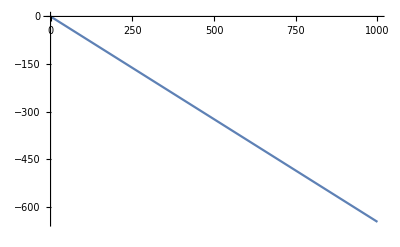

```mathematica
ListLinePlot[table1]
```

```mathematica
Map[wellDataset]
```

```mathematica
wellValues = Table[Values[Normal[wellDataset[Select[#horizon == i&]][[All, {5, 4}]]]], {i, 2, Max[wellDataset[All, 3]]}]
```

{{{0.326972,-234.},{0.321384,-238.},{0.276702,-207.},{0.218562,-181.},{0.192313,-166.},{0.152008,-145.},{0.0854057,-106.},{0.0882691,-93.},{0.0963113,-85.},{0.121279,-33.}},{{0.509991,-336.},{0.50606,-342.},{0.444351,-307.},{0.372536,-286.},{0.339328,-271.},{0.287138,-249.},{0.197512,-208.},{0.195056,-198.},{0.197794,-189.},{0.195821,-140.}},{{0.704405,-438.},{0.711519,-454.},{0.620475,-407.},{0.545209,-401.},{0.499493,-378.},{0.435949,-356.},{0.32956,-322.},{0.321867,-311.},{0.322772,-307.},{0.303868,-270.}}}

```mathematica
Map[wellValues[[All,1]],Times[2]&]
```

```mathematica
Times[2]/@wellValues[[All,All,1]]
```

{2[{0.326972,0.321384,0.276702,0.218562,0.192313,0.152008,0.0854057,0.0882691,0.0963113,0.121279}],2[{0.509991,0.50606,0.444351,0.372536,0.339328,0.287138,0.197512,0.195056,0.197794,0.195821}],2[{0.704405,0.711519,0.620475,0.545209,0.499493,0.435949,0.32956,0.321867,0.322772,0.303868}]}

```mathematica
Map[Times[2#]&,wellValues[[All,All,1]]]
```

{{0.653943,0.642768,0.553403,0.437123,0.384626,0.304015,0.170811,0.176538,0.192623,0.242559},{1.01998,1.01212,0.888702,0.745072,0.678657,0.574276,0.395023,0.390112,0.395589,0.391641},{1.40881,1.42304,1.24095,1.09042,0.998985,0.871898,0.65912,0.643735,0.645544,0.607735}}

```mathematica
Times[wellValues[[All,All,1]] ]
```

{{0.653943,0.642768,0.553403,0.437123,0.384626,0.304015,0.170811,0.176538,0.192623,0.242559},{1.01998,1.01212,0.888702,0.745072,0.678657,0.574276,0.395023,0.390112,0.395589,0.391641},{1.40881,1.42304,1.24095,1.09042,0.998985,0.871898,0.65912,0.643735,0.645544,0.607735}}

```mathematica
wellValues[[All,All,1]]*=2
```

{{1.30789,1.28554,1.10681,0.874246,0.769252,0.608031,0.341623,0.353077,0.385245,0.485117},{2.03996,2.02424,1.7774,1.49014,1.35731,1.14855,0.790047,0.780225,0.791178,0.783283},{2.81762,2.84608,2.4819,2.18084,1.99797,1.7438,1.31824,1.28747,1.29109,1.21547}}

```mathematica
wellValues
```

{{{1.30789,-234.},{1.28554,-238.},{1.10681,-207.},{0.874246,-181.},{0.769252,-166.},{0.608031,-145.},{0.341623,-106.},{0.353077,-93.},{0.385245,-85.},{0.485117,-33.}},{{2.03996,-336.},{2.02424,-342.},{1.7774,-307.},{1.49014,-286.},{1.35731,-271.},{1.14855,-249.},{0.790047,-208.},{0.780225,-198.},{0.791178,-189.},{0.783283,-140.}},{{2.81762,-438.},{2.84608,-454.},{2.4819,-407.},{2.18084,-401.},{1.99797,-378.},{1.7438,-356.},{1.31824,-322.},{1.28747,-311.},{1.29109,-307.},{1.21547,-270.}}}